# Math 223: Homework 5

Ali Heydari

Feb. 25th, 2021

## Problem 1

(a) Find the first three terms in the local behavior as x→ 0^+of a particular solution y(x) to 
y'+xy = x^-3

So now we make certain assumptions about the non-homogenous part and use that to approximate the particular solution. We then check to see which solution is consistent with that assumption:

* First assumption: x^-3≪xy 
y'~xy, so now we can solve this as a homogenous equation:

```mathematica
DSolve[y'[x] - x*y[x] == 0, y[x],x]
```

{{y[x]→ⅇ^(x^2/2) C[1]}}

Now we can check the assumption that we made:

```mathematica
Limit[x^-3/(x*ⅇ^(x^2/2)),x-> 0]
```

∞

which clearly does match with our assumption. So now we move on to the next assumption, where we have:

```mathematica
x y≪ x^-3

which means we have y' ~ x^-3:
```

```mathematica
Limit[(x*-1/2 x^-2)/x^-3,x-> 0]
```

0

which tells us that the last assumption is consistent. So now we can move on to finding a correction to this solution. To do so, we can find a correction term (like the integration constant, but a function of x) with:

y ~ -1/(2 x^2) + C(x),

```mathematica
y'[x]+x y[x]==x^-3 /. y -> Function[x,-1/2 x^-2+c[x]]//FullSimplify
```

2 (x c[x]+c'[x])==1/x

using the same assumption type as before, we assume that xC(x) ≪ x^-1, implying that :
C’(x) ~ 1/(2x) ⇒ C(x) ~ Log[x]/2

so now we can write the particular solution as:

y_p(x) =-1/(2 x^2) + (log(x))/2

and to find the first three terms of the particular solution, we expand this solution about x_0= 0:

```mathematica
Series[-1/(2 x^2) + Log[x]/2,{x,0,3}]
```

-1/(2 x^2)+Log[x]/2+O[x]^4

but this gives us only two terms... however, if we

Now we can check the accuracy of the approximation by checking against the analytical solution.

```mathematica
exactSol = DSolve[y'[x] + x*y[x] == x^-3,y[x],x]
```

{{y[x]→ⅇ^(-x^2/2) C[1]+ⅇ^(-x^2/2) (-(ⅇ^(x^2/2))/(2 x^2)+1/4 ExpIntegralEi[x^2/2])}}

Plotting the particular solution against the approximation :

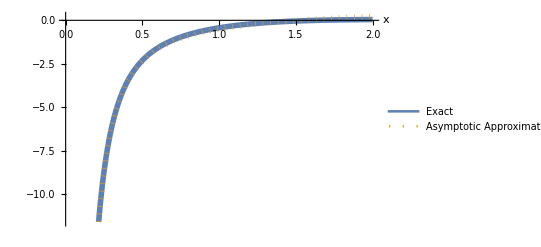

```mathematica
Plot[{ⅇ^(-x^2/2) (-(ⅇ^(x^2/2))/(2 x^2)+1/4 ExpIntegralEi[x^2/2]),-1/(2 x^2)+ Log[x]/2},{x,0,2},PlotStyle->{Directive[Solid,Thickness[0.01]],Directive[Dotted,Thickness[0.01]],Directive[Dashed,Thickness[0.01]]}, PlotLegends->{"Exact", "Asymptotic Approximation"},AxesLabel->Automatic]
```

which looks good, but if we look at the LogPlot, we can see that our solution is actually not that good:

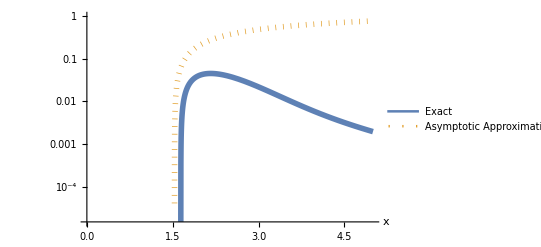

```mathematica
LogPlot[{ⅇ^(-x^2/2) (-(ⅇ^(x^2/2))/(2 x^2)+1/4 ExpIntegralEi[x^2/2]),-1/(2 x^2)+ Log[x]/2},{x,0,5},PlotStyle->{Directive[Solid,Thickness[0.01]],Directive[Dotted,Thickness[0.01]],Directive[Dashed,Thickness[0.01]]}, PlotLegends->{"Exact", "Asymptotic Approximation"},AxesLabel->Automatic]
```

and if we compare Mathematica’s Asymptotic DSolve against the exact solution:

```mathematica
AsymptoticDSolveValue[y'[x] + x*y[x] == x^-3,y[x],{x,0,3}]
```

(1-x^2/2+x^4/8) C[1]+(1-x^2/2+x^4/8) (-1/(2 x^2)+x^2/16+Log[x]/2)

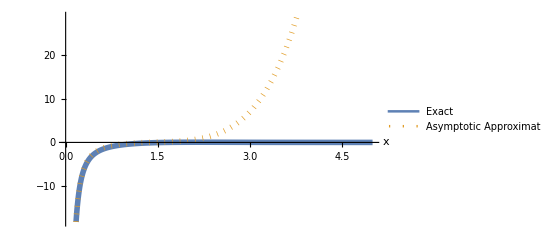

```mathematica
Plot[{ⅇ^(-x^2/2) (-(ⅇ^(x^2/2))/(2 x^2)+1/4 ExpIntegralEi[x^2/2]),(1-x^2/2+x^4/8) (-1/(2 x^2)+x^2/16+Log[x]/2)},{x,0,5},PlotStyle->{Directive[Solid,Thickness[0.01]],Directive[Dotted,Thickness[0.01]],Directive[Dashed,Thickness[0.01]]}, PlotLegends->{"Exact", "Asymptotic Approximation"},AxesLabel->Automatic]
```

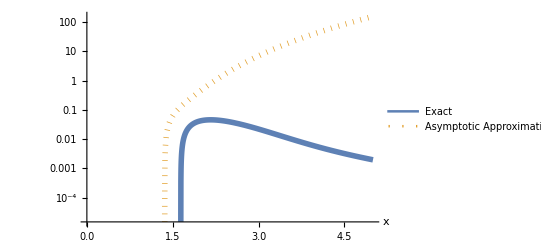

```mathematica
LogPlot[{ⅇ^(-x^2/2) (-(ⅇ^(x^2/2))/(2 x^2)+1/4 ExpIntegralEi[x^2/2]),(1-x^2/2+x^4/8) (-1/(2 x^2)+x^2/16+Log[x]/2)},{x,0,5},PlotStyle->{Directive[Solid,Thickness[0.01]],Directive[Dotted,Thickness[0.01]],Directive[Dashed,Thickness[0.01]]}, PlotLegends->{"Exact", "Asymptotic Approximation"},AxesLabel->Automatic]
```

so I guess compared to this, our method of dominant balance performs better qualitatively?

(b) Find the leading behavior of (∫_0)^1 ⅇ^-xt/(1+t)^2 dt as x → 0^+

The idea here is to find the asymptotic behavior of the integral by considering the asymptotic behavior of the integrand (as individual functions). So we notice that the integral has the form:
∫_a^b ζ(x,t)ⅆt, as x→0^+,
in other words, x happens to be a parameter since the integration is in terms of change in t. Therefore, if we can find an asymptotic relation for ζ  just in terms of t, i.e. if we find some holomorphic function ψ(t) that is asymptotically equivalent, then we can express the integrand as 

ζ(x,t) = ψ_0(t) + (x-(0))^n ψ_1(t)+(x-(0))^(2n)ψ_2(t)  + ⋯ for some n uniformly in a≤ t ≤b. 

Once we have found such asymptotic expansion, then we can integrate term by term until the desired accuracy is achieved. 

Looking back at the given problem, we can check to see if the expansion will have a constant term as the leading term:

```mathematica
Series[ Exp[-x * t]/(1+t)^2,{x,0,5}]
```

1/(1+t)^2-(t x)/(1+t)^2+(t^2 x^2)/(2 (1+t)^2)-(t^3 x^3)/(6 (1+t)^2)+(t^4 x^4)/(24 (1+t)^2)-(t^5 x^5)/(120 (1+t)^2)+O[x]^6

Which is does not. So we can just take the integral of this expansion, say the first two terms, and for an interval of a=0 ≤ t ≤b=1:

```mathematica
behavior = Integrate[ Collect[Series[ Exp[-x * t]/(1+t)^2,{x,0,2}],x],{t,0,1}]
```

1/4 (2+x (2+3 x-4 (1+x) Log[2]))

now to check the solution:

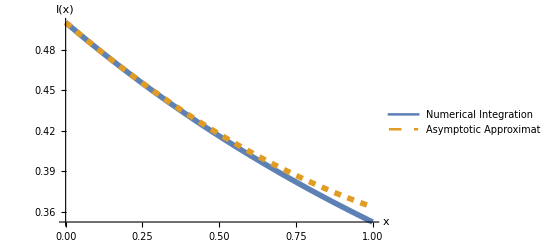

```mathematica
Plot[{NIntegrate[Exp[-x * t]/(1+t)^2,{t,0,1}],behavior},{x,0,1},PlotStyle->{Directive[Solid,Thickness[0.01]],Directive[Dashed,Thickness[0.01]]}, AxesLabel->{Style["x",Italic,18],Style["I(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Numerical Integration", "Asymptotic Approximation"}]
```

And if we want to make this more accurate, we can just take more terms:

```mathematica
betterApprox = Integrate[ Collect[Series[ Exp[-x * t]/(1+t)^2,{x,0,5}],x],{t,0,1}]
```

1/2+(x (-720 (-1+Log[4])+x (x (x (170+41 x-60 (4+x) Log[2])-240 (-2+Log[8]))-360 (-3+Log[16]))))/1440

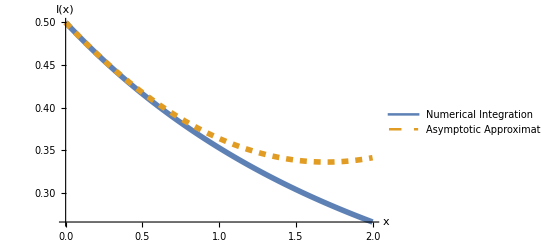

```mathematica
Plot[{NIntegrate[Exp[-x * t]/(1+t)^2,{t,0,1}],behavior},{x,0,2},PlotStyle->{Directive[Solid,Thickness[0.01]],Directive[Dashed,Thickness[0.01]]}, AxesLabel->{Style["x",Italic,18],Style["I(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Numerical Integration", "Asymptotic Approximation"}]
```

To see the difference better:

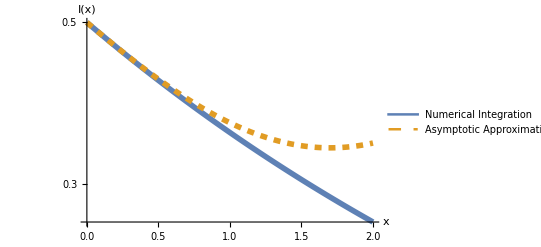

```mathematica
LogPlot[{NIntegrate[Exp[-x * t]/(1+t)^2,{t,0,1}],behavior},{x,0,2},PlotStyle->{Directive[Solid,Thickness[0.01]],Directive[Dashed,Thickness[0.01]]}, AxesLabel->{Style["x",Italic,18],Style["I(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Numerical Integration", "Asymptotic Approximation"}]
```

which seems good for x ∈ [0,1], but  it does much worse as we get further away from 0. Also, it is important to note that these results are for a very small value of t, and increasing these window could also yield worse approximations.

(c) Find the asymptotic series series for (∫_0)^x t^(-1/4)ⅇ^-t dt, x→ 0^+